## A little formula to show what is always there, what sometimes and what is never

```mathematica
ShowAlwaysSometimesNever[sols_,always_]:=Block[{all,   syms, parts,alwaysparts, byRank=Association[], alwaysbyRank=Association[], level,pos, sym, sympos, sets, type,k=Total[First  [sols]]},
Table[
byRank[rank]={};
alwaysbyRank[rank]={}
,{rank,k}];

For[pos=1,pos<=Length[sols],pos++,
sets=sols[[pos]];
level=Length[sets];
byRank[level]=DeleteDuplicates[Append[byRank[level],sets]]
];
For[pos=1,pos<=Length[always],pos++,
sets=always[[pos]];
level=Length[sets];
alwaysbyRank[level]=DeleteDuplicates[Append[alwaysbyRank[level],sets]]
];

(* filter*)
Monitor[
Table[
parts=Association[];
syms=byRank[rank];
For [sympos=1,sympos≤ Length[syms],sympos++,
type=syms[[sympos]];
parts[type]=1
];

alwaysparts=Association[];
syms=alwaysbyRank[rank];
For [sympos=1,sympos≤ Length[syms],sympos++,
type=syms[[sympos]];
alwaysparts[type]=1
];

all=IntegerPartitions[k,{rank}];
Labeled[
Grid[
Table[
If[KeyExistsQ[parts,row],
If[KeyExistsQ[alwaysparts,row],
Map[Style[#,Darker[Green],Bold]&,row],
Map[Style[#,Blue]&,row]],
Map[Style[#,Red]&,row]]
,{row,all}
],
Frame->All
],
rank
]
,{rank,k}
],
{rank,k}
]
]
```

```mathematica
Calcalways[sols_]:=Block[{
max=Max[Map[#[[2]]&,sols]]},
Map[First,Select[sols,#[[2]]==max&]]
]
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[countTable_]:=ShowAlwaysSometimesNever[Map[First,countTable],Calcalways[countTable]]
```

```mathematica
CalcNever[sols_]:=Block[{
size=Total[First[First[sols]]],all, never, part},
all=IntegerPartitions[size];
part=DeleteDuplicates[Map[First,sols]];
Select[all,!MemberQ[part,#]&]
]
```

## This has been calculated in the cloud

We define a set for each count

```mathematica
doc14={{{5,5,4},23},{{6,4,4},5},{{6,5,3},3},{{6,6,2},1},{{4,4,3,3},257660},{{4,4,4,2},124697},{{5,3,3,3},132751},{{5,4,3,2},187577},{{5,4,4,1},14129},{{5,5,2,2},10350},{{5,5,3,1},4509},{{6,3,3,2},16881},{{6,4,2,2},6152},{{6,4,3,1},2229},{{6,5,2,1},216},{{6,6,1,1},2},{{7,3,2,2},136},{{7,3,3,1},12},{{7,4,2,1},6},{{8,2,2,2},1},{{3,3,3,3,2},336922},{{4,3,3,2,2},337440},{{4,3,3,3,1},339099},{{4,4,2,2,2},337419},{{4,4,3,2,1},339700},{{4,4,4,1,1},195271},{{5,3,2,2,2},291369},{{5,3,3,2,1},294159},{{5,4,2,2,1},257273},{{5,4,3,1,1},234258},{{5,5,2,1,1},26195},{{6,2,2,2,2},49151},{{6,3,2,2,1},54836},{{6,3,3,1,1},35794},{{6,4,2,1,1},17582},{{6,5,1,1,1},387},{{7,2,2,2,1},884},{{7,3,2,1,1},668},{{7,4,1,1,1},31},{{8,2,2,1,1},2},{{3,3,2,2,2,2},337440},{{3,3,3,2,2,1},339721},{{3,3,3,3,1,1},339722},{{4,2,2,2,2,2},337440},{{4,3,2,2,2,1},339721},{{4,3,3,2,1,1},339722},{{4,4,2,2,1,1},339701},{{4,4,3,1,1,1},339701},{{5,2,2,2,2,1},294198},{{5,3,2,2,1,1},294199},{{5,3,3,1,1,1},294163},{{5,4,2,1,1,1},257650},{{5,5,1,1,1,1},26806},{{6,2,2,2,1,1},55080},{{6,3,2,1,1,1},54851},{{6,4,1,1,1,1},17918},{{7,2,2,1,1,1},940},{{7,3,1,1,1,1},694},{{8,2,1,1,1,1},2},{{2,2,2,2,2,2,2},337440},{{3,2,2,2,2,2,1},339721},{{3,3,2,2,2,1,1},339722},{{3,3,3,2,1,1,1},339722},{{4,2,2,2,2,1,1},339722},{{4,3,2,2,1,1,1},339722},{{4,3,3,1,1,1,1},339722},{{4,4,2,1,1,1,1},339701},{{5,2,2,2,1,1,1},294199},{{5,3,2,1,1,1,1},294199},{{5,4,1,1,1,1,1},257650},{{6,2,2,1,1,1,1},55080},{{6,3,1,1,1,1,1},54851},{{7,2,1,1,1,1,1},940},{{8,1,1,1,1,1,1},2},{{2,2,2,2,2,2,1,1},339722},{{3,2,2,2,2,1,1,1},339722},{{3,3,2,2,1,1,1,1},339722},{{3,3,3,1,1,1,1,1},339722},{{4,2,2,2,1,1,1,1},339722},{{4,3,2,1,1,1,1,1},339722},{{4,4,1,1,1,1,1,1},339701},{{5,2,2,1,1,1,1,1},294199},{{5,3,1,1,1,1,1,1},294199},{{6,2,1,1,1,1,1,1},55080},{{7,1,1,1,1,1,1,1},940},{{2,2,2,2,2,1,1,1,1},339722},{{3,2,2,2,1,1,1,1,1},339722},{{3,3,2,1,1,1,1,1,1},339722},{{4,2,2,1,1,1,1,1,1},339722},{{4,3,1,1,1,1,1,1,1},339722},{{5,2,1,1,1,1,1,1,1},294199},{{6,1,1,1,1,1,1,1,1},55080},{{2,2,2,2,1,1,1,1,1,1},339722},{{3,2,2,1,1,1,1,1,1,1},339722},{{3,3,1,1,1,1,1,1,1,1},339722},{{4,2,1,1,1,1,1,1,1,1},339722},{{5,1,1,1,1,1,1,1,1,1},294199},{{2,2,2,1,1,1,1,1,1,1,1},339722},{{3,2,1,1,1,1,1,1,1,1,1},339722},{{4,1,1,1,1,1,1,1,1,1,1},339722},{{2,2,1,1,1,1,1,1,1,1,1,1},339722},{{3,1,1,1,1,1,1,1,1,1,1,1},339722},{{2,1,1,1,1,1,1,1,1,1,1,1,1},339722},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},339722}};
```

```mathematica
always14=Calcalways[doc14];
```

```mathematica
never14=CalcNever[doc14];
```

```mathematica
never14
```

{{14},{13,1},{12,2},{12,1,1},{11,3},{11,2,1},{11,1,1,1},{10,4},{10,3,1},{10,2,2},{10,2,1,1},{10,1,1,1,1},{9,5},{9,4,1},{9,3,2},{9,3,1,1},{9,2,2,1},{9,2,1,1,1},{9,1,1,1,1,1},{8,6},{8,5,1},{8,4,2},{8,4,1,1},{8,3,3},{8,3,2,1},{8,3,1,1,1},{7,7},{7,6,1},{7,5,2},{7,5,1,1},{7,4,3}}

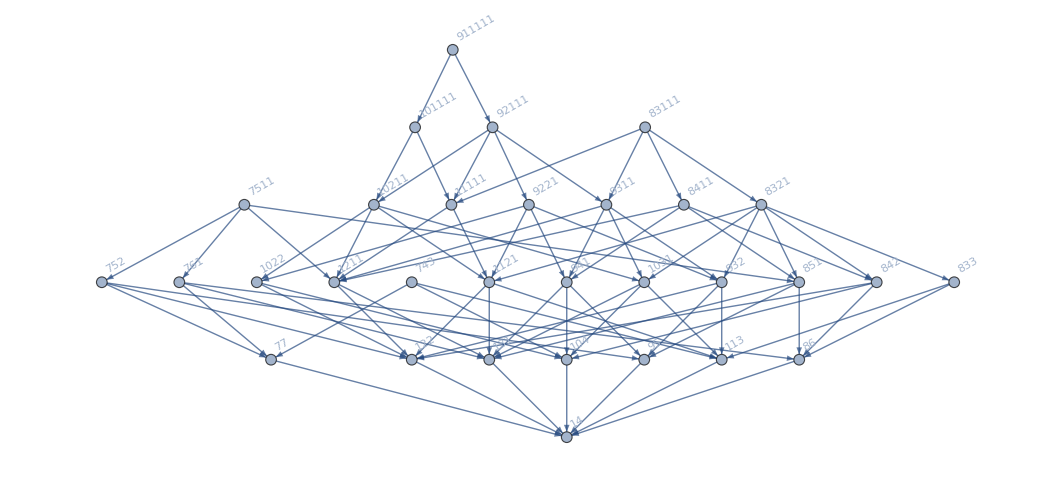

```mathematica
Graph[PartitionTypeLattice[never14],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[#->Rotate[PartitionTypeLabel[#],Pi/6]&,never14]]
```

```mathematica
IntegerPartitions[14,{1,7}]
```

{{14},{13,1},{12,2},{12,1,1},{11,3},{11,2,1},{11,1,1,1},{10,4},{10,3,1},{10,2,2},{10,2,1,1},{10,1,1,1,1},{9,5},{9,4,1},{9,3,2},{9,3,1,1},{9,2,2,1},{9,2,1,1,1},{9,1,1,1,1,1},{8,6},{8,5,1},{8,4,2},{8,4,1,1},{8,3,3},{8,3,2,1},{8,3,1,1,1},{8,2,2,2},{8,2,2,1,1},{8,2,1,1,1,1},{8,1,1,1,1,1,1},{7,7},{7,6,1},{7,5,2},{7,5,1,1},{7,4,3},{7,4,2,1},{7,4,1,1,1},{7,3,3,1},{7,3,2,2},{7,3,2,1,1},{7,3,1,1,1,1},{7,2,2,2,1},{7,2,2,1,1,1},{7,2,1,1,1,1,1},{6,6,2},{6,6,1,1},{6,5,3},{6,5,2,1},{6,5,1,1,1},{6,4,4},{6,4,3,1},{6,4,2,2},{6,4,2,1,1},{6,4,1,1,1,1},{6,3,3,2},{6,3,3,1,1},{6,3,2,2,1},{6,3,2,1,1,1},{6,3,1,1,1,1,1},{6,2,2,2,2},{6,2,2,2,1,1},{6,2,2,1,1,1,1},{5,5,4},{5,5,3,1},{5,5,2,2},{5,5,2,1,1},{5,5,1,1,1,1},{5,4,4,1},{5,4,3,2},{5,4,3,1,1},{5,4,2,2,1},{5,4,2,1,1,1},{5,4,1,1,1,1,1},{5,3,3,3},{5,3,3,2,1},{5,3,3,1,1,1},{5,3,2,2,2},{5,3,2,2,1,1},{5,3,2,1,1,1,1},{5,2,2,2,2,1},{5,2,2,2,1,1,1},{4,4,4,2},{4,4,4,1,1},{4,4,3,3},{4,4,3,2,1},{4,4,3,1,1,1},{4,4,2,2,2},{4,4,2,2,1,1},{4,4,2,1,1,1,1},{4,3,3,3,1},{4,3,3,2,2},{4,3,3,2,1,1},{4,3,3,1,1,1,1},{4,3,2,2,2,1},{4,3,2,2,1,1,1},{4,2,2,2,2,2},{4,2,2,2,2,1,1},{3,3,3,3,2},{3,3,3,3,1,1},{3,3,3,2,2,1},{3,3,3,2,1,1,1},{3,3,2,2,2,2},{3,3,2,2,2,1,1},{3,2,2,2,2,2,1},{2,2,2,2,2,2,2}}

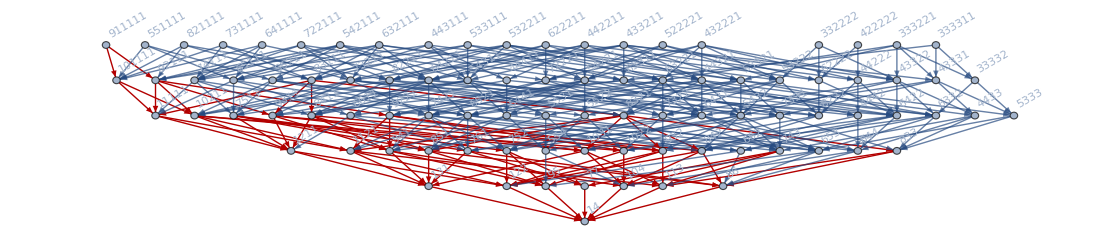

```mathematica
With[{all=IntegerPartitions[14,{1,6}],never=CalcNever[doc14]},
Graph[PartitionTypeLattice[all],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[#->Rotate[PartitionTypeLabel[#],Pi/6]&,all],GraphHighlight->PartitionTypeLattice[never]]
]
```

```mathematica
Max[Map[Total,CalcNever[doc14]]]
```

14

```mathematica
BaseForm[14,2]
```

1110_2

```mathematica
PrettyLattic[doc_]:=Block[{coll=doc, height, never,size,all, neverLattice, roots, neverGraph},
never = CalcNever[coll];
height=Max[Map[Length,never]];
size=Max[Map[Total,never]];
all=IntegerPartitions[size,{1,height}];
neverLattice=PartitionTypeLattice[never];
neverGraph=Graph[neverLattice];
roots=Select[VertexList[neverGraph],VertexInDegree[neverGraph,#]==0&];
Rotate[
Graph[
PartitionTypeLattice[all],
GraphLayout->"LayeredDigraphEmbedding", 
VertexLabels->Map[#->Rotate[Framed[PartitionTypeLabel[#], Background->If[MemberQ[roots,#],LightYellow,White]],-Pi/2]&,all],
GraphHighlight->Join[never,neverLattice] ,
GraphHighlightStyle->"Thick", 
ImageSize->{500,Automatic},
AspectRatio->GoldenRatio, 
VertexStyle->Map[#->Darker[Green]&,Select[all,Length[#]==4&]]],Pi/2]
]
```

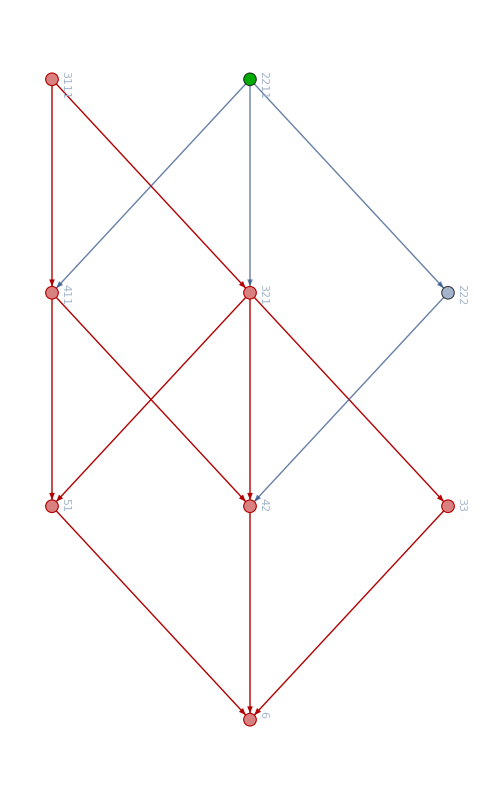
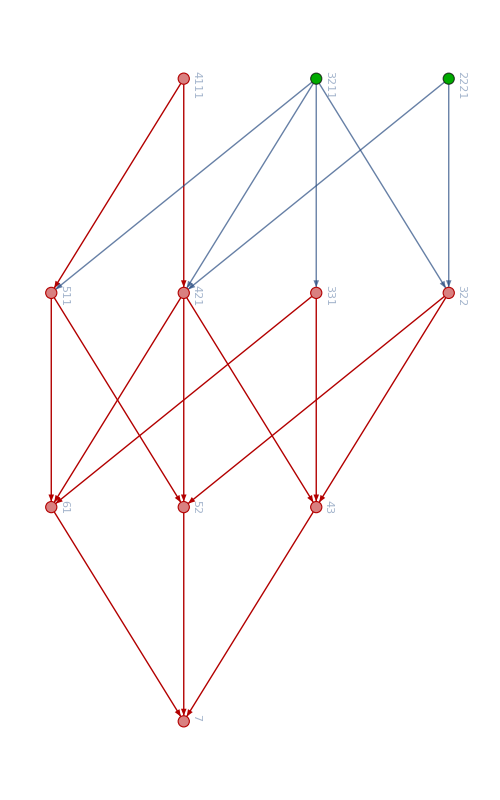
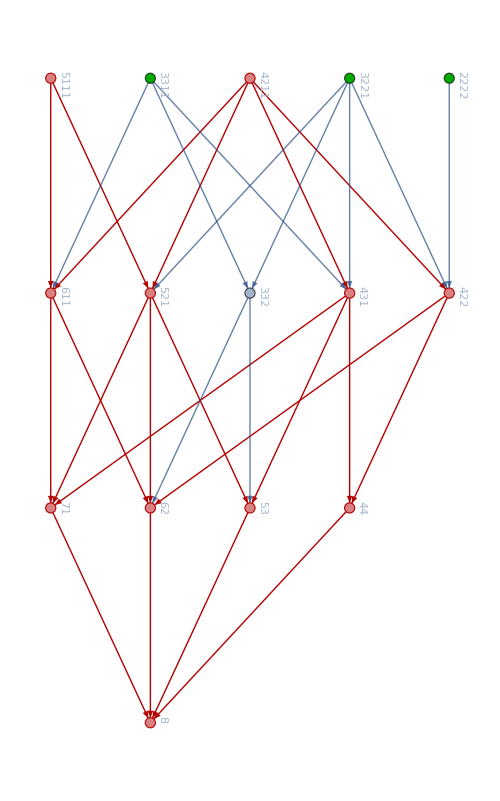
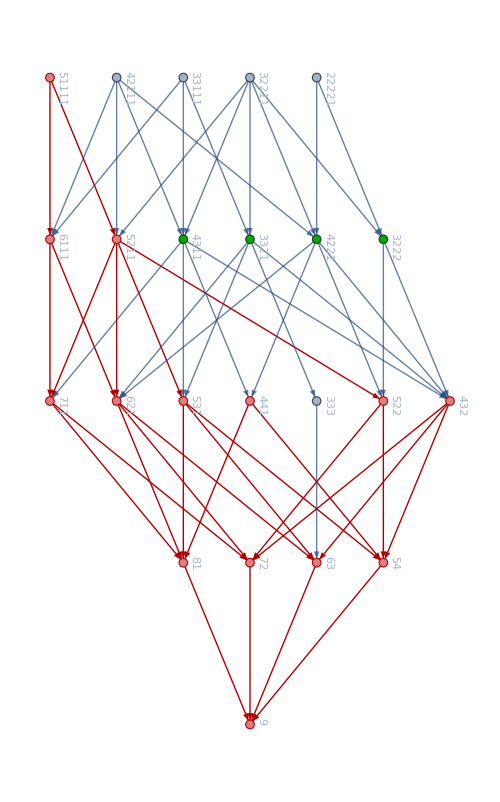

```mathematica
Table[PrettyLattic[d],{d,{doc6,doc7,doc8,doc9}}]
```

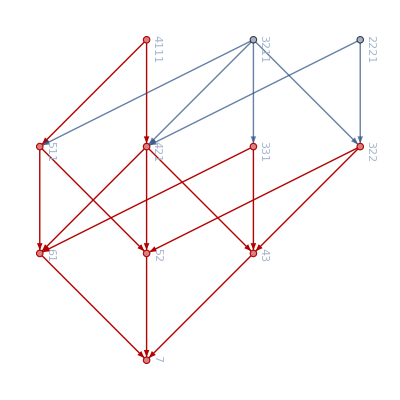

```mathematica
Block[{coll=doc7, height, never,size,all},
never = CalcNever[coll];
height=Max[Map[Length,never]];
size=Max[Map[Total,never]];
all=IntegerPartitions[size,{1,height}];
Rotate[Graph[PartitionTypeLattice[all],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[#->Rotate[Framed[PartitionTypeLabel[#], Background->White],-Pi/2]&,all],GraphHighlight->Join[never,PartitionTypeLattice[never]] ,GraphHighlightStyle->"Thick"],Pi/2]
]
```

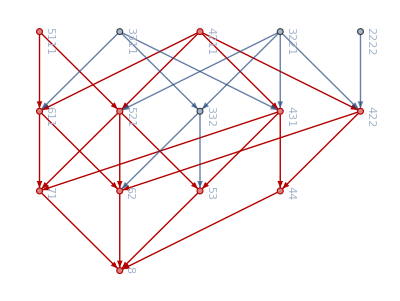

```mathematica
Block[{coll=doc8, height, never,size,all},
never = CalcNever[coll];
height=Max[Map[Length,never]];
size=Max[Map[Total,never]];
all=IntegerPartitions[size,{1,height}];
Rotate[Graph[PartitionTypeLattice[all],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[#->Rotate[Framed[PartitionTypeLabel[#], Background->White],-Pi/2]&,all],GraphHighlight->Join[never,PartitionTypeLattice[never]] ,GraphHighlightStyle->"Thick"],Pi/2]
]
```

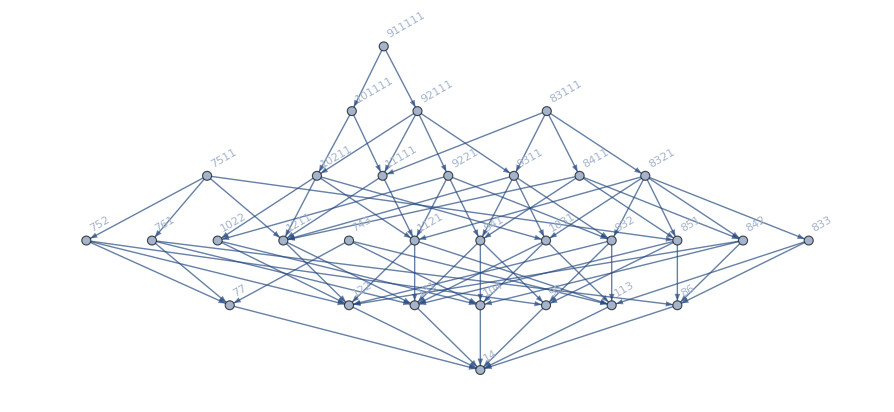

```mathematica
With[{never=CalcNever[doc14]},
Graph[PartitionTypeLattice[never],GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[#->Rotate[PartitionTypeLabel[#],Pi/6]&,never]]
]
```

```mathematica
Sort[always14,Variance[#1]<Variance[#2]&]
```

{{1,1,1,1,1,1,1,1,1,1,1,1,1,1},{2,1,1,1,1,1,1,1,1,1,1,1,1},{2,2,1,1,1,1,1,1,1,1,1,1},{2,2,2,2,2,2,1,1},{2,2,2,1,1,1,1,1,1,1,1},{2,2,2,2,1,1,1,1,1,1},{2,2,2,2,2,1,1,1,1},{3,1,1,1,1,1,1,1,1,1,1,1},{3,2,1,1,1,1,1,1,1,1,1},{3,2,2,1,1,1,1,1,1,1},{3,2,2,2,2,1,1,1},{3,2,2,2,1,1,1,1,1},{3,3,2,2,2,1,1},{3,3,1,1,1,1,1,1,1,1},{3,3,2,1,1,1,1,1,1},{3,3,2,2,1,1,1,1},{4,1,1,1,1,1,1,1,1,1,1},{4,2,1,1,1,1,1,1,1,1},{4,2,2,2,2,1,1},{3,3,3,2,1,1,1},{4,2,2,1,1,1,1,1,1},{3,3,3,3,1,1},{4,2,2,2,1,1,1,1},{3,3,3,1,1,1,1,1},{4,3,1,1,1,1,1,1,1},{4,3,2,2,1,1,1},{4,3,2,1,1,1,1,1},{4,3,3,2,1,1},{4,3,3,1,1,1,1}}

```mathematica
Map[Variance,Sort[IntegerPartitions[15,{6}],Variance[#1]<Variance[#2]&]]
```

{3/10,7/10,7/10,11/10,3/2,3/2,3/2,19/10,19/10,23/10,27/10,27/10,31/10,31/10,7/2,39/10,39/10,43/10,51/10,11/2,11/2,63/10,15/2,79/10,103/10,27/2}

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc14]
```

{141,13 | 1
12 | 2
11 | 3
10 | 4
9 | 5
8 | 6
7 | 72,12 | 1 | 1
11 | 2 | 1
10 | 3 | 1
10 | 2 | 2
9 | 4 | 1
9 | 3 | 2
8 | 5 | 1
8 | 4 | 2
8 | 3 | 3
7 | 6 | 1
7 | 5 | 2
7 | 4 | 3
6 | 6 | 2
6 | 5 | 3
6 | 4 | 4
5 | 5 | 43,11 | 1 | 1 | 1
10 | 2 | 1 | 1
9 | 3 | 1 | 1
9 | 2 | 2 | 1
8 | 4 | 1 | 1
8 | 3 | 2 | 1
8 | 2 | 2 | 2
7 | 5 | 1 | 1
7 | 4 | 2 | 1
7 | 3 | 3 | 1
7 | 3 | 2 | 2
6 | 6 | 1 | 1
6 | 5 | 2 | 1
6 | 4 | 3 | 1
6 | 4 | 2 | 2
6 | 3 | 3 | 2
5 | 5 | 3 | 1
5 | 5 | 2 | 2
5 | 4 | 4 | 1
5 | 4 | 3 | 2
5 | 3 | 3 | 3
4 | 4 | 4 | 2
4 | 4 | 3 | 34,10 | 1 | 1 | 1 | 1
9 | 2 | 1 | 1 | 1
8 | 3 | 1 | 1 | 1
8 | 2 | 2 | 1 | 1
7 | 4 | 1 | 1 | 1
7 | 3 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1
6 | 5 | 1 | 1 | 1
6 | 4 | 2 | 1 | 1
6 | 3 | 3 | 1 | 1
6 | 3 | 2 | 2 | 1
6 | 2 | 2 | 2 | 2
5 | 5 | 2 | 1 | 1
5 | 4 | 3 | 1 | 1
5 | 4 | 2 | 2 | 1
5 | 3 | 3 | 2 | 1
5 | 3 | 2 | 2 | 2
4 | 4 | 4 | 1 | 1
4 | 4 | 3 | 2 | 1
4 | 4 | 2 | 2 | 2
4 | 3 | 3 | 3 | 1
4 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 25,9 | 1 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1 | 1
6 | 4 | 1 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1 | 1
6 | 2 | 2 | 2 | 1 | 1
5 | 5 | 1 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1 | 1
5 | 3 | 3 | 1 | 1 | 1
5 | 3 | 2 | 2 | 1 | 1
5 | 2 | 2 | 2 | 2 | 1
4 | 4 | 3 | 1 | 1 | 1
4 | 4 | 2 | 2 | 1 | 1
4 | 3 | 3 | 2 | 1 | 1
4 | 3 | 2 | 2 | 2 | 1
4 | 2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 1 | 1
3 | 3 | 3 | 2 | 2 | 1
3 | 3 | 2 | 2 | 2 | 26,8 | 1 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1 | 1
3 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1 | 1
3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 2 | 27,7 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 1 | 18,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 19,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 110,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 114}

```mathematica
doc13={{{5,4,4},5},{{5,5,3},3},{{4,3,3,3},32276},{{4,4,3,2},35754},{{4,4,4,1},1935},{{5,3,3,2},15918},{{5,4,2,2},6269},{{5,4,3,1},2953},{{5,5,2,1},128},{{6,3,2,2},520},{{6,3,3,1},82},{{6,4,2,1},39},{{6,5,1,1},1},{{7,2,2,2},2},{{3,3,3,2,2},48833},{{3,3,3,3,1},49074},{{4,3,2,2,2},48833},{{4,3,3,2,1},49565},{{4,4,2,2,1},46633},{{4,4,3,1,1},43603},{{5,2,2,2,2},28662},{{5,3,2,2,1},30044},{{5,3,3,1,1},24835},{{5,4,2,1,1},12300},{{5,5,1,1,1},232},{{6,2,2,2,1},2005},{{6,3,2,1,1},1673},{{6,4,1,1,1},111},{{7,2,2,1,1},9},{{7,3,1,1,1},1},{{3,2,2,2,2,2},48833},{{3,3,2,2,2,1},49565},{{3,3,3,2,1,1},49566},{{4,2,2,2,2,1},49565},{{4,3,2,2,1,1},49566},{{4,3,3,1,1,1},49566},{{4,4,2,1,1,1},46635},{{5,2,2,2,1,1},30063},{{5,3,2,1,1,1},30045},{{5,4,1,1,1,1},12398},{{6,2,2,1,1,1},2065},{{6,3,1,1,1,1},1695},{{7,2,1,1,1,1},9},{{2,2,2,2,2,2,1},49565},{{3,2,2,2,2,1,1},49566},{{3,3,2,2,1,1,1},49566},{{3,3,3,1,1,1,1},49566},{{4,2,2,2,1,1,1},49566},{{4,3,2,1,1,1,1},49566},{{4,4,1,1,1,1,1},46635},{{5,2,2,1,1,1,1},30063},{{5,3,1,1,1,1,1},30045},{{6,2,1,1,1,1,1},2065},{{7,1,1,1,1,1,1},9},{{2,2,2,2,2,1,1,1},49566},{{3,2,2,2,1,1,1,1},49566},{{3,3,2,1,1,1,1,1},49566},{{4,2,2,1,1,1,1,1},49566},{{4,3,1,1,1,1,1,1},49566},{{5,2,1,1,1,1,1,1},30063},{{6,1,1,1,1,1,1,1},2065},{{2,2,2,2,1,1,1,1,1},49566},{{3,2,2,1,1,1,1,1,1},49566},{{3,3,1,1,1,1,1,1,1},49566},{{4,2,1,1,1,1,1,1,1},49566},{{5,1,1,1,1,1,1,1,1},30063},{{2,2,2,1,1,1,1,1,1,1},49566},{{3,2,1,1,1,1,1,1,1,1},49566},{{4,1,1,1,1,1,1,1,1,1},49566},{{2,2,1,1,1,1,1,1,1,1,1},49566},{{3,1,1,1,1,1,1,1,1,1,1},49566},{{2,1,1,1,1,1,1,1,1,1,1,1},49566},{{1,1,1,1,1,1,1,1,1,1,1,1,1},49566}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc13]
```

{131,12 | 1
11 | 2
10 | 3
9 | 4
8 | 5
7 | 62,11 | 1 | 1
10 | 2 | 1
9 | 3 | 1
9 | 2 | 2
8 | 4 | 1
8 | 3 | 2
7 | 5 | 1
7 | 4 | 2
7 | 3 | 3
6 | 6 | 1
6 | 5 | 2
6 | 4 | 3
5 | 5 | 3
5 | 4 | 43,10 | 1 | 1 | 1
9 | 2 | 1 | 1
8 | 3 | 1 | 1
8 | 2 | 2 | 1
7 | 4 | 1 | 1
7 | 3 | 2 | 1
7 | 2 | 2 | 2
6 | 5 | 1 | 1
6 | 4 | 2 | 1
6 | 3 | 3 | 1
6 | 3 | 2 | 2
5 | 5 | 2 | 1
5 | 4 | 3 | 1
5 | 4 | 2 | 2
5 | 3 | 3 | 2
4 | 4 | 4 | 1
4 | 4 | 3 | 2
4 | 3 | 3 | 34,9 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1
6 | 4 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1
6 | 2 | 2 | 2 | 1
5 | 5 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1
5 | 3 | 3 | 1 | 1
5 | 3 | 2 | 2 | 1
5 | 2 | 2 | 2 | 2
4 | 4 | 3 | 1 | 1
4 | 4 | 2 | 2 | 1
4 | 3 | 3 | 2 | 1
4 | 3 | 2 | 2 | 2
3 | 3 | 3 | 3 | 1
3 | 3 | 3 | 2 | 25,8 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1
3 | 3 | 3 | 2 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1
3 | 2 | 2 | 2 | 2 | 26,7 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 17,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 18,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 19,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 110,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113}

```mathematica
doc12={{{4,4,4},5},{{5,4,3},2},{{5,5,2},1},{{3,3,3,3},3111},{{4,3,3,2},6439},{{4,4,2,2},2000},{{4,4,3,1},947},{{5,3,2,2},963},{{5,3,3,1},213},{{5,4,2,1},105},{{5,5,1,1},2},{{6,2,2,2},10},{{6,3,2,1},2},{{3,3,2,2,2},7367},{{3,3,3,2,1},7594},{{4,2,2,2,2},7275},{{4,3,2,2,1},7502},{{4,3,3,1,1},7342},{{4,4,2,1,1},3757},{{5,2,2,2,1},2216},{{5,3,2,1,1},1991},{{5,4,1,1,1},169},{{6,2,2,1,1},45},{{6,3,1,1,1},11},{{2,2,2,2,2,2},7367},{{3,2,2,2,2,1},7594},{{3,3,2,2,1,1},7595},{{3,3,3,1,1,1},7595},{{4,2,2,2,1,1},7503},{{4,3,2,1,1,1},7503},{{4,4,1,1,1,1},3785},{{5,2,2,1,1,1},2221},{{5,3,1,1,1,1},1997},{{6,2,1,1,1,1},45},{{2,2,2,2,2,1,1},7595},{{3,2,2,2,1,1,1},7595},{{3,3,2,1,1,1,1},7595},{{4,2,2,1,1,1,1},7503},{{4,3,1,1,1,1,1},7503},{{5,2,1,1,1,1,1},2221},{{6,1,1,1,1,1,1},45},{{2,2,2,2,1,1,1,1},7595},{{3,2,2,1,1,1,1,1},7595},{{3,3,1,1,1,1,1,1},7595},{{4,2,1,1,1,1,1,1},7503},{{5,1,1,1,1,1,1,1},2221},{{2,2,2,1,1,1,1,1,1},7595},{{3,2,1,1,1,1,1,1,1},7595},{{4,1,1,1,1,1,1,1,1},7503},{{2,2,1,1,1,1,1,1,1,1},7595},{{3,1,1,1,1,1,1,1,1,1},7595},{{2,1,1,1,1,1,1,1,1,1,1},7595},{{1,1,1,1,1,1,1,1,1,1,1,1},7595}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc12]
```

{121,11 | 1
10 | 2
9 | 3
8 | 4
7 | 5
6 | 62,10 | 1 | 1
9 | 2 | 1
8 | 3 | 1
8 | 2 | 2
7 | 4 | 1
7 | 3 | 2
6 | 5 | 1
6 | 4 | 2
6 | 3 | 3
5 | 5 | 2
5 | 4 | 3
4 | 4 | 43,9 | 1 | 1 | 1
8 | 2 | 1 | 1
7 | 3 | 1 | 1
7 | 2 | 2 | 1
6 | 4 | 1 | 1
6 | 3 | 2 | 1
6 | 2 | 2 | 2
5 | 5 | 1 | 1
5 | 4 | 2 | 1
5 | 3 | 3 | 1
5 | 3 | 2 | 2
4 | 4 | 3 | 1
4 | 4 | 2 | 2
4 | 3 | 3 | 2
3 | 3 | 3 | 34,8 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1
5 | 4 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1
5 | 2 | 2 | 2 | 1
4 | 4 | 2 | 1 | 1
4 | 3 | 3 | 1 | 1
4 | 3 | 2 | 2 | 1
4 | 2 | 2 | 2 | 2
3 | 3 | 3 | 2 | 1
3 | 3 | 2 | 2 | 25,7 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 26,6 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 17,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 18,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 19,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112}

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc14]
```

{141,13 | 1
12 | 2
11 | 3
10 | 4
9 | 5
8 | 6
7 | 72,12 | 1 | 1
11 | 2 | 1
10 | 3 | 1
10 | 2 | 2
9 | 4 | 1
9 | 3 | 2
8 | 5 | 1
8 | 4 | 2
8 | 3 | 3
7 | 6 | 1
7 | 5 | 2
7 | 4 | 3
6 | 6 | 2
6 | 5 | 3
6 | 4 | 4
5 | 5 | 43,11 | 1 | 1 | 1
10 | 2 | 1 | 1
9 | 3 | 1 | 1
9 | 2 | 2 | 1
8 | 4 | 1 | 1
8 | 3 | 2 | 1
8 | 2 | 2 | 2
7 | 5 | 1 | 1
7 | 4 | 2 | 1
7 | 3 | 3 | 1
7 | 3 | 2 | 2
6 | 6 | 1 | 1
6 | 5 | 2 | 1
6 | 4 | 3 | 1
6 | 4 | 2 | 2
6 | 3 | 3 | 2
5 | 5 | 3 | 1
5 | 5 | 2 | 2
5 | 4 | 4 | 1
5 | 4 | 3 | 2
5 | 3 | 3 | 3
4 | 4 | 4 | 2
4 | 4 | 3 | 34,10 | 1 | 1 | 1 | 1
9 | 2 | 1 | 1 | 1
8 | 3 | 1 | 1 | 1
8 | 2 | 2 | 1 | 1
7 | 4 | 1 | 1 | 1
7 | 3 | 2 | 1 | 1
7 | 2 | 2 | 2 | 1
6 | 5 | 1 | 1 | 1
6 | 4 | 2 | 1 | 1
6 | 3 | 3 | 1 | 1
6 | 3 | 2 | 2 | 1
6 | 2 | 2 | 2 | 2
5 | 5 | 2 | 1 | 1
5 | 4 | 3 | 1 | 1
5 | 4 | 2 | 2 | 1
5 | 3 | 3 | 2 | 1
5 | 3 | 2 | 2 | 2
4 | 4 | 4 | 1 | 1
4 | 4 | 3 | 2 | 1
4 | 4 | 2 | 2 | 2
4 | 3 | 3 | 3 | 1
4 | 3 | 3 | 2 | 2
3 | 3 | 3 | 3 | 25,9 | 1 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1 | 1
6 | 4 | 1 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1 | 1
6 | 2 | 2 | 2 | 1 | 1
5 | 5 | 1 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1 | 1
5 | 3 | 3 | 1 | 1 | 1
5 | 3 | 2 | 2 | 1 | 1
5 | 2 | 2 | 2 | 2 | 1
4 | 4 | 3 | 1 | 1 | 1
4 | 4 | 2 | 2 | 1 | 1
4 | 3 | 3 | 2 | 1 | 1
4 | 3 | 2 | 2 | 2 | 1
4 | 2 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 1 | 1
3 | 3 | 3 | 2 | 2 | 1
3 | 3 | 2 | 2 | 2 | 26,8 | 1 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1 | 1
3 | 3 | 3 | 2 | 1 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1 | 1
3 | 2 | 2 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 2 | 2 | 27,7 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 1 | 18,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 19,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 110,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 114}

```mathematica
doc11={{{4,4,3},2},{{3,3,3,2},883},{{4,3,2,2},785},{{4,3,3,1},258},{{4,4,2,1},61},{{5,2,2,2},31},{{5,3,2,1},16},{{5,4,1,1},1},{{3,2,2,2,2},1167},{{3,3,2,2,1},1248},{{3,3,3,1,1},1185},{{4,2,2,2,1},1076},{{4,3,2,1,1},1040},{{4,4,1,1,1},99},{{5,2,2,1,1},110},{{5,3,1,1,1},39},{{6,2,1,1,1},1},{{2,2,2,2,2,1},1248},{{3,2,2,2,1,1},1249},{{3,3,2,1,1,1},1249},{{4,2,2,1,1,1},1077},{{4,3,1,1,1,1},1040},{{5,2,1,1,1,1},110},{{6,1,1,1,1,1},1},{{2,2,2,2,1,1,1},1249},{{3,2,2,1,1,1,1},1249},{{3,3,1,1,1,1,1},1249},{{4,2,1,1,1,1,1},1077},{{5,1,1,1,1,1,1},110},{{2,2,2,1,1,1,1,1},1249},{{3,2,1,1,1,1,1,1},1249},{{4,1,1,1,1,1,1,1},1077},{{2,2,1,1,1,1,1,1,1},1249},{{3,1,1,1,1,1,1,1,1},1249},{{2,1,1,1,1,1,1,1,1,1},1249},{{1,1,1,1,1,1,1,1,1,1,1},1249}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc11]
```

{111,10 | 1
9 | 2
8 | 3
7 | 4
6 | 52,9 | 1 | 1
8 | 2 | 1
7 | 3 | 1
7 | 2 | 2
6 | 4 | 1
6 | 3 | 2
5 | 5 | 1
5 | 4 | 2
5 | 3 | 3
4 | 4 | 33,8 | 1 | 1 | 1
7 | 2 | 1 | 1
6 | 3 | 1 | 1
6 | 2 | 2 | 1
5 | 4 | 1 | 1
5 | 3 | 2 | 1
5 | 2 | 2 | 2
4 | 4 | 2 | 1
4 | 3 | 3 | 1
4 | 3 | 2 | 2
3 | 3 | 3 | 24,7 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1
4 | 4 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1
4 | 2 | 2 | 2 | 1
3 | 3 | 3 | 1 | 1
3 | 3 | 2 | 2 | 1
3 | 2 | 2 | 2 | 25,6 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 16,5 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 17,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 18,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 19,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 111}

```mathematica
Map[First,Select[doc11,#[[2]]==1249&]]//Length
```

11

```mathematica
doc10={{{4,3,3},1},{{4,4,2},1},{{3,3,2,2},194},{{3,3,3,1},50},{{4,2,2,2},62},{{4,3,2,1},42},{{4,4,1,1},2},{{5,2,2,1},1},{{2,2,2,2,2},206},{{3,2,2,2,1},232},{{3,3,2,1,1},232},{{4,2,2,1,1},125},{{4,3,1,1,1},59},{{5,2,1,1,1},3},{{2,2,2,2,1,1},233},{{3,2,2,1,1,1},233},{{3,3,1,1,1,1},232},{{4,2,1,1,1,1},125},{{5,1,1,1,1,1},3},{{2,2,2,1,1,1,1},233},{{3,2,1,1,1,1,1},233},{{4,1,1,1,1,1,1},125},{{2,2,1,1,1,1,1,1},233},{{3,1,1,1,1,1,1,1},233},{{2,1,1,1,1,1,1,1,1},233},{{1,1,1,1,1,1,1,1,1,1},233}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc10]
```

{101,9 | 1
8 | 2
7 | 3
6 | 4
5 | 52,8 | 1 | 1
7 | 2 | 1
6 | 3 | 1
6 | 2 | 2
5 | 4 | 1
5 | 3 | 2
4 | 4 | 2
4 | 3 | 33,7 | 1 | 1 | 1
6 | 2 | 1 | 1
5 | 3 | 1 | 1
5 | 2 | 2 | 1
4 | 4 | 1 | 1
4 | 3 | 2 | 1
4 | 2 | 2 | 2
3 | 3 | 3 | 1
3 | 3 | 2 | 24,6 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1
3 | 3 | 2 | 1 | 1
3 | 2 | 2 | 2 | 1
2 | 2 | 2 | 2 | 25,5 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 16,4 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 17,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 18,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 110}

```mathematica
Map[First,Select[doc10,#[[2]]==233&]]//Length
```

8

```mathematica
doc9={{{3,3,3},1},{{3,2,2,2},38},{{3,3,2,1},24},{{4,2,2,1},4},{{4,3,1,1},1},{{2,2,2,2,1},49},{{3,2,2,1,1},50},{{3,3,1,1,1},32},{{4,2,1,1,1},10},{{2,2,2,1,1,1},50},{{3,2,1,1,1,1},50},{{4,1,1,1,1,1},10},{{2,2,1,1,1,1,1},50},{{3,1,1,1,1,1,1},50},{{2,1,1,1,1,1,1,1},50},{{1,1,1,1,1,1,1,1,1},50}};
```

```mathematica
Map[First,Select[doc9,#[[2]]==50&]]//Length
```

7

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc9]
```

{91,8 | 1
7 | 2
6 | 3
5 | 42,7 | 1 | 1
6 | 2 | 1
5 | 3 | 1
5 | 2 | 2
4 | 4 | 1
4 | 3 | 2
3 | 3 | 33,6 | 1 | 1 | 1
5 | 2 | 1 | 1
4 | 3 | 1 | 1
4 | 2 | 2 | 1
3 | 3 | 2 | 1
3 | 2 | 2 | 24,5 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 15,4 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 16,3 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 17,2 | 1 | 1 | 1 | 1 | 1 | 1 | 18,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 19}

```mathematica
doc8={{{3,3,2},1},{{2,2,2,2},10},{{3,2,2,1},8},{{3,3,1,1},2},{{2,2,2,1,1},14},{{3,2,1,1,1},11},{{4,1,1,1,1},1},{{2,2,1,1,1,1},14},{{3,1,1,1,1,1},11},{{2,1,1,1,1,1,1},14},{{1,1,1,1,1,1,1,1},14}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc8]
```

{81,7 | 1
6 | 2
5 | 3
4 | 42,6 | 1 | 1
5 | 2 | 1
4 | 3 | 1
4 | 2 | 2
3 | 3 | 23,5 | 1 | 1 | 1
4 | 2 | 1 | 1
3 | 3 | 1 | 1
3 | 2 | 2 | 1
2 | 2 | 2 | 24,4 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1
2 | 2 | 2 | 1 | 15,3 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 16,2 | 1 | 1 | 1 | 1 | 1 | 17,1 | 1 | 1 | 1 | 1 | 1 | 1 | 18}

```mathematica
doc7={{{2,2,2,1},4},{{3,2,1,1},1},{{2,2,1,1,1},5},{{3,1,1,1,1},2},{{2,1,1,1,1,1},5},{{1,1,1,1,1,1,1},5}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc7]
```

{71,6 | 1
5 | 2
4 | 32,5 | 1 | 1
4 | 2 | 1
3 | 3 | 1
3 | 2 | 23,4 | 1 | 1 | 1
3 | 2 | 1 | 1
2 | 2 | 2 | 14,3 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 15,2 | 1 | 1 | 1 | 1 | 16,1 | 1 | 1 | 1 | 1 | 1 | 17}

```mathematica
doc6={{{2,2,2},1},{{2,2,1,1},2},{{2,1,1,1,1},2},{{1,1,1,1,1,1},2}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc6]
```

{61,5 | 1
4 | 2
3 | 32,4 | 1 | 1
3 | 2 | 1
2 | 2 | 23,3 | 1 | 1 | 1
2 | 2 | 1 | 14,2 | 1 | 1 | 1 | 15,1 | 1 | 1 | 1 | 1 | 16}

```mathematica
doc5={{{2,1,1,1},1},{{1,1,1,1,1},1}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc5]
```

{51,4 | 1
3 | 22,3 | 1 | 1
2 | 2 | 13,2 | 1 | 1 | 14,1 | 1 | 1 | 1 | 15}

## The following is not based on complete data

```mathematica
doc15={{{4,4,4,3},1346},{{5,4,3,3},1545},{{5,4,4,2},888},{{5,5,3,2},456},{{5,5,4,1},56},{{6,3,3,3},187},{{6,4,3,2},318},{{6,4,4,1},15},{{6,5,2,2},28},{{6,5,3,1},15},{{7,3,3,2},8},{{7,4,2,2},3},{{3,3,3,3,3},1856},{{4,3,3,3,2},1994},{{4,4,3,2,2},1994},{{4,4,3,3,1},2000},{{4,4,4,2,1},1992},{{5,3,3,2,2},1959},{{5,3,3,3,1},1965},{{5,4,2,2,2},1951},{{5,4,3,2,1},1957},{{5,4,4,1,1},1199},{{5,5,2,2,1},879},{{5,5,3,1,1},717},{{6,3,2,2,2},783},{{6,3,3,2,1},797},{{6,4,2,2,1},634},{{6,4,3,1,1},505},{{6,5,2,1,1},65},{{7,2,2,2,2},38},{{7,3,2,2,1},49},{{7,3,3,1,1},26},{{7,4,2,1,1},15},{{7,5,1,1,1},1},{{3,3,3,2,2,2},1994},{{3,3,3,3,2,1},2000},{{4,3,2,2,2,2},1994},{{4,3,3,2,2,1},2000},{{4,3,3,3,1,1},2000},{{4,4,2,2,2,1},2000},{{4,4,3,2,1,1},2000},{{4,4,4,1,1,1},1992},{{5,2,2,2,2,2},1959},{{5,3,2,2,2,1},1965},{{5,3,3,2,1,1},1965},{{5,4,2,2,1,1},1957},{{5,4,3,1,1,1},1957},{{5,5,2,1,1,1},893},{{6,2,2,2,2,1},799},{{6,3,2,2,1,1},799},{{6,3,3,1,1,1},797},{{6,4,2,1,1,1},637},{{6,5,1,1,1,1},66},{{7,2,2,2,1,1},49},{{7,3,2,1,1,1},49},{{7,4,1,1,1,1},15},{{3,2,2,2,2,2,2},1994},{{3,3,2,2,2,2,1},2000},{{3,3,3,2,2,1,1},2000},{{3,3,3,3,1,1,1},2000},{{4,2,2,2,2,2,1},2000},{{4,3,2,2,2,1,1},2000},{{4,3,3,2,1,1,1},2000},{{4,4,2,2,1,1,1},2000},{{4,4,3,1,1,1,1},2000},{{5,2,2,2,2,1,1},1965},{{5,3,2,2,1,1,1},1965},{{5,3,3,1,1,1,1},1965},{{5,4,2,1,1,1,1},1957},{{5,5,1,1,1,1,1},893},{{6,2,2,2,1,1,1},799},{{6,3,2,1,1,1,1},799},{{6,4,1,1,1,1,1},637},{{7,2,2,1,1,1,1},49},{{7,3,1,1,1,1,1},49},{{2,2,2,2,2,2,2,1},2000},{{3,2,2,2,2,2,1,1},2000},{{3,3,2,2,2,1,1,1},2000},{{3,3,3,2,1,1,1,1},2000},{{4,2,2,2,2,1,1,1},2000},{{4,3,2,2,1,1,1,1},2000},{{4,3,3,1,1,1,1,1},2000},{{4,4,2,1,1,1,1,1},2000},{{5,2,2,2,1,1,1,1},1965},{{5,3,2,1,1,1,1,1},1965},{{5,4,1,1,1,1,1,1},1957},{{6,2,2,1,1,1,1,1},799},{{6,3,1,1,1,1,1,1},799},{{7,2,1,1,1,1,1,1},49},{{2,2,2,2,2,2,1,1,1},2000},{{3,2,2,2,2,1,1,1,1},2000},{{3,3,2,2,1,1,1,1,1},2000},{{3,3,3,1,1,1,1,1,1},2000},{{4,2,2,2,1,1,1,1,1},2000},{{4,3,2,1,1,1,1,1,1},2000},{{4,4,1,1,1,1,1,1,1},2000},{{5,2,2,1,1,1,1,1,1},1965},{{5,3,1,1,1,1,1,1,1},1965},{{6,2,1,1,1,1,1,1,1},799},{{7,1,1,1,1,1,1,1,1},49},{{2,2,2,2,2,1,1,1,1,1},2000},{{3,2,2,2,1,1,1,1,1,1},2000},{{3,3,2,1,1,1,1,1,1,1},2000},{{4,2,2,1,1,1,1,1,1,1},2000},{{4,3,1,1,1,1,1,1,1,1},2000},{{5,2,1,1,1,1,1,1,1,1},1965},{{6,1,1,1,1,1,1,1,1,1},799},{{2,2,2,2,1,1,1,1,1,1,1},2000},{{3,2,2,1,1,1,1,1,1,1,1},2000},{{3,3,1,1,1,1,1,1,1,1,1},2000},{{4,2,1,1,1,1,1,1,1,1,1},2000},{{5,1,1,1,1,1,1,1,1,1,1},1965},{{2,2,2,1,1,1,1,1,1,1,1,1},2000},{{3,2,1,1,1,1,1,1,1,1,1,1},2000},{{4,1,1,1,1,1,1,1,1,1,1,1},2000},{{2,2,1,1,1,1,1,1,1,1,1,1,1},2000},{{3,1,1,1,1,1,1,1,1,1,1,1,1},2000},{{2,1,1,1,1,1,1,1,1,1,1,1,1,1},2000},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},2000}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[doc15]
```

{151,14 | 1
13 | 2
12 | 3
11 | 4
10 | 5
9 | 6
8 | 72,13 | 1 | 1
12 | 2 | 1
11 | 3 | 1
11 | 2 | 2
10 | 4 | 1
10 | 3 | 2
9 | 5 | 1
9 | 4 | 2
9 | 3 | 3
8 | 6 | 1
8 | 5 | 2
8 | 4 | 3
7 | 7 | 1
7 | 6 | 2
7 | 5 | 3
7 | 4 | 4
6 | 6 | 3
6 | 5 | 4
5 | 5 | 53,12 | 1 | 1 | 1
11 | 2 | 1 | 1
10 | 3 | 1 | 1
10 | 2 | 2 | 1
9 | 4 | 1 | 1
9 | 3 | 2 | 1
9 | 2 | 2 | 2
8 | 5 | 1 | 1
8 | 4 | 2 | 1
8 | 3 | 3 | 1
8 | 3 | 2 | 2
7 | 6 | 1 | 1
7 | 5 | 2 | 1
7 | 4 | 3 | 1
7 | 4 | 2 | 2
7 | 3 | 3 | 2
6 | 6 | 2 | 1
6 | 5 | 3 | 1
6 | 5 | 2 | 2
6 | 4 | 4 | 1
6 | 4 | 3 | 2
6 | 3 | 3 | 3
5 | 5 | 4 | 1
5 | 5 | 3 | 2
5 | 4 | 4 | 2
5 | 4 | 3 | 3
4 | 4 | 4 | 34,11 | 1 | 1 | 1 | 1
10 | 2 | 1 | 1 | 1
9 | 3 | 1 | 1 | 1
9 | 2 | 2 | 1 | 1
8 | 4 | 1 | 1 | 1
8 | 3 | 2 | 1 | 1
8 | 2 | 2 | 2 | 1
7 | 5 | 1 | 1 | 1
7 | 4 | 2 | 1 | 1
7 | 3 | 3 | 1 | 1
7 | 3 | 2 | 2 | 1
7 | 2 | 2 | 2 | 2
6 | 6 | 1 | 1 | 1
6 | 5 | 2 | 1 | 1
6 | 4 | 3 | 1 | 1
6 | 4 | 2 | 2 | 1
6 | 3 | 3 | 2 | 1
6 | 3 | 2 | 2 | 2
5 | 5 | 3 | 1 | 1
5 | 5 | 2 | 2 | 1
5 | 4 | 4 | 1 | 1
5 | 4 | 3 | 2 | 1
5 | 4 | 2 | 2 | 2
5 | 3 | 3 | 3 | 1
5 | 3 | 3 | 2 | 2
4 | 4 | 4 | 2 | 1
4 | 4 | 3 | 3 | 1
4 | 4 | 3 | 2 | 2
4 | 3 | 3 | 3 | 2
3 | 3 | 3 | 3 | 35,10 | 1 | 1 | 1 | 1 | 1
9 | 2 | 1 | 1 | 1 | 1
8 | 3 | 1 | 1 | 1 | 1
8 | 2 | 2 | 1 | 1 | 1
7 | 4 | 1 | 1 | 1 | 1
7 | 3 | 2 | 1 | 1 | 1
7 | 2 | 2 | 2 | 1 | 1
6 | 5 | 1 | 1 | 1 | 1
6 | 4 | 2 | 1 | 1 | 1
6 | 3 | 3 | 1 | 1 | 1
6 | 3 | 2 | 2 | 1 | 1
6 | 2 | 2 | 2 | 2 | 1
5 | 5 | 2 | 1 | 1 | 1
5 | 4 | 3 | 1 | 1 | 1
5 | 4 | 2 | 2 | 1 | 1
5 | 3 | 3 | 2 | 1 | 1
5 | 3 | 2 | 2 | 2 | 1
5 | 2 | 2 | 2 | 2 | 2
4 | 4 | 4 | 1 | 1 | 1
4 | 4 | 3 | 2 | 1 | 1
4 | 4 | 2 | 2 | 2 | 1
4 | 3 | 3 | 3 | 1 | 1
4 | 3 | 3 | 2 | 2 | 1
4 | 3 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 2 | 1
3 | 3 | 3 | 2 | 2 | 26,9 | 1 | 1 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1 | 1 | 1
6 | 4 | 1 | 1 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1 | 1 | 1
6 | 2 | 2 | 2 | 1 | 1 | 1
5 | 5 | 1 | 1 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1 | 1 | 1
5 | 3 | 3 | 1 | 1 | 1 | 1
5 | 3 | 2 | 2 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 1 | 1
4 | 4 | 3 | 1 | 1 | 1 | 1
4 | 4 | 2 | 2 | 1 | 1 | 1
4 | 3 | 3 | 2 | 1 | 1 | 1
4 | 3 | 2 | 2 | 2 | 1 | 1
4 | 2 | 2 | 2 | 2 | 2 | 1
3 | 3 | 3 | 3 | 1 | 1 | 1
3 | 3 | 3 | 2 | 2 | 1 | 1
3 | 3 | 2 | 2 | 2 | 2 | 1
3 | 2 | 2 | 2 | 2 | 2 | 27,8 | 1 | 1 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1 | 1 | 1
3 | 3 | 3 | 2 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 18,7 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 19,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 110,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 111,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 114,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 115}

```mathematica
docs15b={{{4,4,4,3},2606},{{5,4,3,3},2929},{{5,4,4,2},1706},{{5,5,3,2},808},{{5,5,4,1},107},{{6,3,3,3},373},{{6,4,3,2},583},{{6,4,4,1},32},{{6,5,2,2},47},{{6,5,3,1},26},{{7,3,3,2},10},{{7,4,2,2},3},{{3,3,3,3,3},3539},{{4,3,3,3,2},3812},{{4,4,3,2,2},3812},{{4,4,3,3,1},3824},{{4,4,4,2,1},3808},{{5,3,3,2,2},3737},{{5,3,3,3,1},3749},{{5,4,2,2,2},3725},{{5,4,3,2,1},3737},{{5,4,4,1,1},2316},{{5,5,2,2,1},1671},{{5,5,3,1,1},1330},{{6,3,2,2,2},1505},{{6,3,3,2,1},1521},{{6,4,2,2,1},1209},{{6,4,3,1,1},961},{{6,5,2,1,1},114},{{7,2,2,2,2},63},{{7,3,2,2,1},80},{{7,3,3,1,1},39},{{7,4,2,1,1},22},{{7,5,1,1,1},1},{{3,3,3,2,2,2},3812},{{3,3,3,3,2,1},3824},{{4,3,2,2,2,2},3812},{{4,3,3,2,2,1},3824},{{4,3,3,3,1,1},3824},{{4,4,2,2,2,1},3824},{{4,4,3,2,1,1},3824},{{4,4,4,1,1,1},3808},{{5,2,2,2,2,2},3737},{{5,3,2,2,2,1},3749},{{5,3,3,2,1,1},3749},{{5,4,2,2,1,1},3737},{{5,4,3,1,1,1},3737},{{5,5,2,1,1,1},1698},{{6,2,2,2,2,1},1532},{{6,3,2,2,1,1},1532},{{6,3,3,1,1,1},1521},{{6,4,2,1,1,1},1214},{{6,5,1,1,1,1},116},{{7,2,2,2,1,1},80},{{7,3,2,1,1,1},80},{{7,4,1,1,1,1},23},{{3,2,2,2,2,2,2},3812},{{3,3,2,2,2,2,1},3824},{{3,3,3,2,2,1,1},3824},{{3,3,3,3,1,1,1},3824},{{4,2,2,2,2,2,1},3824},{{4,3,2,2,2,1,1},3824},{{4,3,3,2,1,1,1},3824},{{4,4,2,2,1,1,1},3824},{{4,4,3,1,1,1,1},3824},{{5,2,2,2,2,1,1},3749},{{5,3,2,2,1,1,1},3749},{{5,3,3,1,1,1,1},3749},{{5,4,2,1,1,1,1},3737},{{5,5,1,1,1,1,1},1698},{{6,2,2,2,1,1,1},1532},{{6,3,2,1,1,1,1},1532},{{6,4,1,1,1,1,1},1214},{{7,2,2,1,1,1,1},80},{{7,3,1,1,1,1,1},80},{{2,2,2,2,2,2,2,1},3824},{{3,2,2,2,2,2,1,1},3824},{{3,3,2,2,2,1,1,1},3824},{{3,3,3,2,1,1,1,1},3824},{{4,2,2,2,2,1,1,1},3824},{{4,3,2,2,1,1,1,1},3824},{{4,3,3,1,1,1,1,1},3824},{{4,4,2,1,1,1,1,1},3824},{{5,2,2,2,1,1,1,1},3749},{{5,3,2,1,1,1,1,1},3749},{{5,4,1,1,1,1,1,1},3737},{{6,2,2,1,1,1,1,1},1532},{{6,3,1,1,1,1,1,1},1532},{{7,2,1,1,1,1,1,1},80},{{2,2,2,2,2,2,1,1,1},3824},{{3,2,2,2,2,1,1,1,1},3824},{{3,3,2,2,1,1,1,1,1},3824},{{3,3,3,1,1,1,1,1,1},3824},{{4,2,2,2,1,1,1,1,1},3824},{{4,3,2,1,1,1,1,1,1},3824},{{4,4,1,1,1,1,1,1,1},3824},{{5,2,2,1,1,1,1,1,1},3749},{{5,3,1,1,1,1,1,1,1},3749},{{6,2,1,1,1,1,1,1,1},1532},{{7,1,1,1,1,1,1,1,1},80},{{2,2,2,2,2,1,1,1,1,1},3824},{{3,2,2,2,1,1,1,1,1,1},3824},{{3,3,2,1,1,1,1,1,1,1},3824},{{4,2,2,1,1,1,1,1,1,1},3824},{{4,3,1,1,1,1,1,1,1,1},3824},{{5,2,1,1,1,1,1,1,1,1},3749},{{6,1,1,1,1,1,1,1,1,1},1532},{{2,2,2,2,1,1,1,1,1,1,1},3824},{{3,2,2,1,1,1,1,1,1,1,1},3824},{{3,3,1,1,1,1,1,1,1,1,1},3824},{{4,2,1,1,1,1,1,1,1,1,1},3824},{{5,1,1,1,1,1,1,1,1,1,1},3749},{{2,2,2,1,1,1,1,1,1,1,1,1},3824},{{3,2,1,1,1,1,1,1,1,1,1,1},3824},{{4,1,1,1,1,1,1,1,1,1,1,1},3824},{{2,2,1,1,1,1,1,1,1,1,1,1,1},3824},{{3,1,1,1,1,1,1,1,1,1,1,1,1},3824},{{2,1,1,1,1,1,1,1,1,1,1,1,1,1},3824},{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},3824}};
```

```mathematica
ShowAlwaysSometimesNeverFromCountTable[docs15b]
```

{151,14 | 1
13 | 2
12 | 3
11 | 4
10 | 5
9 | 6
8 | 72,13 | 1 | 1
12 | 2 | 1
11 | 3 | 1
11 | 2 | 2
10 | 4 | 1
10 | 3 | 2
9 | 5 | 1
9 | 4 | 2
9 | 3 | 3
8 | 6 | 1
8 | 5 | 2
8 | 4 | 3
7 | 7 | 1
7 | 6 | 2
7 | 5 | 3
7 | 4 | 4
6 | 6 | 3
6 | 5 | 4
5 | 5 | 53,12 | 1 | 1 | 1
11 | 2 | 1 | 1
10 | 3 | 1 | 1
10 | 2 | 2 | 1
9 | 4 | 1 | 1
9 | 3 | 2 | 1
9 | 2 | 2 | 2
8 | 5 | 1 | 1
8 | 4 | 2 | 1
8 | 3 | 3 | 1
8 | 3 | 2 | 2
7 | 6 | 1 | 1
7 | 5 | 2 | 1
7 | 4 | 3 | 1
7 | 4 | 2 | 2
7 | 3 | 3 | 2
6 | 6 | 2 | 1
6 | 5 | 3 | 1
6 | 5 | 2 | 2
6 | 4 | 4 | 1
6 | 4 | 3 | 2
6 | 3 | 3 | 3
5 | 5 | 4 | 1
5 | 5 | 3 | 2
5 | 4 | 4 | 2
5 | 4 | 3 | 3
4 | 4 | 4 | 34,11 | 1 | 1 | 1 | 1
10 | 2 | 1 | 1 | 1
9 | 3 | 1 | 1 | 1
9 | 2 | 2 | 1 | 1
8 | 4 | 1 | 1 | 1
8 | 3 | 2 | 1 | 1
8 | 2 | 2 | 2 | 1
7 | 5 | 1 | 1 | 1
7 | 4 | 2 | 1 | 1
7 | 3 | 3 | 1 | 1
7 | 3 | 2 | 2 | 1
7 | 2 | 2 | 2 | 2
6 | 6 | 1 | 1 | 1
6 | 5 | 2 | 1 | 1
6 | 4 | 3 | 1 | 1
6 | 4 | 2 | 2 | 1
6 | 3 | 3 | 2 | 1
6 | 3 | 2 | 2 | 2
5 | 5 | 3 | 1 | 1
5 | 5 | 2 | 2 | 1
5 | 4 | 4 | 1 | 1
5 | 4 | 3 | 2 | 1
5 | 4 | 2 | 2 | 2
5 | 3 | 3 | 3 | 1
5 | 3 | 3 | 2 | 2
4 | 4 | 4 | 2 | 1
4 | 4 | 3 | 3 | 1
4 | 4 | 3 | 2 | 2
4 | 3 | 3 | 3 | 2
3 | 3 | 3 | 3 | 35,10 | 1 | 1 | 1 | 1 | 1
9 | 2 | 1 | 1 | 1 | 1
8 | 3 | 1 | 1 | 1 | 1
8 | 2 | 2 | 1 | 1 | 1
7 | 4 | 1 | 1 | 1 | 1
7 | 3 | 2 | 1 | 1 | 1
7 | 2 | 2 | 2 | 1 | 1
6 | 5 | 1 | 1 | 1 | 1
6 | 4 | 2 | 1 | 1 | 1
6 | 3 | 3 | 1 | 1 | 1
6 | 3 | 2 | 2 | 1 | 1
6 | 2 | 2 | 2 | 2 | 1
5 | 5 | 2 | 1 | 1 | 1
5 | 4 | 3 | 1 | 1 | 1
5 | 4 | 2 | 2 | 1 | 1
5 | 3 | 3 | 2 | 1 | 1
5 | 3 | 2 | 2 | 2 | 1
5 | 2 | 2 | 2 | 2 | 2
4 | 4 | 4 | 1 | 1 | 1
4 | 4 | 3 | 2 | 1 | 1
4 | 4 | 2 | 2 | 2 | 1
4 | 3 | 3 | 3 | 1 | 1
4 | 3 | 3 | 2 | 2 | 1
4 | 3 | 2 | 2 | 2 | 2
3 | 3 | 3 | 3 | 2 | 1
3 | 3 | 3 | 2 | 2 | 26,9 | 1 | 1 | 1 | 1 | 1 | 1
8 | 2 | 1 | 1 | 1 | 1 | 1
7 | 3 | 1 | 1 | 1 | 1 | 1
7 | 2 | 2 | 1 | 1 | 1 | 1
6 | 4 | 1 | 1 | 1 | 1 | 1
6 | 3 | 2 | 1 | 1 | 1 | 1
6 | 2 | 2 | 2 | 1 | 1 | 1
5 | 5 | 1 | 1 | 1 | 1 | 1
5 | 4 | 2 | 1 | 1 | 1 | 1
5 | 3 | 3 | 1 | 1 | 1 | 1
5 | 3 | 2 | 2 | 1 | 1 | 1
5 | 2 | 2 | 2 | 2 | 1 | 1
4 | 4 | 3 | 1 | 1 | 1 | 1
4 | 4 | 2 | 2 | 1 | 1 | 1
4 | 3 | 3 | 2 | 1 | 1 | 1
4 | 3 | 2 | 2 | 2 | 1 | 1
4 | 2 | 2 | 2 | 2 | 2 | 1
3 | 3 | 3 | 3 | 1 | 1 | 1
3 | 3 | 3 | 2 | 2 | 1 | 1
3 | 3 | 2 | 2 | 2 | 2 | 1
3 | 2 | 2 | 2 | 2 | 2 | 27,8 | 1 | 1 | 1 | 1 | 1 | 1 | 1
7 | 2 | 1 | 1 | 1 | 1 | 1 | 1
6 | 3 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 2 | 1 | 1 | 1 | 1 | 1
5 | 4 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 2 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 2 | 1 | 1 | 1 | 1
4 | 4 | 2 | 1 | 1 | 1 | 1 | 1
4 | 3 | 3 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 2 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 2 | 1 | 1 | 1
3 | 3 | 3 | 2 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 2 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 2 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 2 | 18,7 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
6 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 4 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 3 | 3 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 2 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 2 | 1 | 1 | 19,6 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
5 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 110,5 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 111,4 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
3 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 112,3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 113,2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 114,1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 115}

```mathematica
Select[Map[First,docs15],!MemberQ[Map[First,docs15b],#]&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[docs15,!MemberQ[First/@docs15b,#1]&].

Select[docs15,!MemberQ[First/@docs15b,#1]&]